Null^3

-Graphics3D-

-Graphics3D-

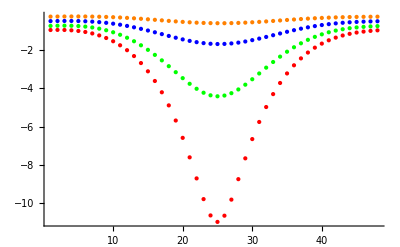

-Graphics3D-

```mathematica
(*Poisson solver that implements the first part of the algorithm described below - it represents the Laplacian as a matrix operator then inverts it. Any solution to Poisson's equation is now found by multiplying the inverse matrix by the (forcing function ρ? idk if you can call it that)*)
(*This is a symmetric finite difference method to solve the Poisson Equation*) 
(*en.wikipedia.org/wiki/Discrete_Poisson_equation*)
Clear[MM,NN,n,α] 


MM=49;(*Increases accuracy*)(*should be odd to have wire over a line of charge*)
NN=25;(*Pulls it back*)

(*construct D, the matrix operator that corresponds to the Laplacian. This is a 9 point stencil*)
periodicblock[a_,b_]:=a IdentityMatrix[MM-1]+DiagonalMatrix[Table[b,{i,0,MM-3}],1]+DiagonalMatrix[Table[b,{i,0,MM-3}],-1]+DiagonalMatrix[{b},-MM+2]+DiagonalMatrix[{b},MM-2];
m1 = periodicblock[-2./3,-1/6];
m2 = periodicblock[10/3,-2/3];
m3 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN}],{0}],0],m2];

m4 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN-1}],{0}],1],m1];
m5 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN-1}],{0}],-1],m1];
m6 =KroneckerProduct[DiagonalMatrix[{1},NN],m1];
m7=1/2 IdentityMatrix[MM-1];
m8 =KroneckerProduct[DiagonalMatrix[{0,1},-NN+1],m7];
m9=KroneckerProduct[DiagonalMatrix[Join[Table[0,{i,1,NN}],{1}],0],-m7];
m = m3+m4+m5+m6+m8+m9;
newm=m3+m4+m5;


ϵ1=10;
ϵ2=5;
H=12;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
α=(.529)/a;(*Subscript[a, 0]/a, where Subscript[a, 0] is the Bohr radius*)
Ry=13.60569253;(*Rydberg unit of energy, in eV*)
λ=10;(*electrons per unit cell*)


totalCharge= -(ϵ2/ϵ1)(λ/N[π])ArcTan[(MM a)/(2H)];

chargeDist[x_,y_]:=-Sin[(π y)/MM]Exp[-(2π x)/MM];

tempTotal = Table[
 N[chargeDist[i ,j ]],
{i,1,NN},
{j,1,MM-1}
]//Flatten//Total;

n[x_,y_]:=-(8N[π]Ry α)/ϵ2 N[chargeDist[x,y]]/tempTotal totalCharge;(*If[x==Floor[1/2 NN stepSize],0/(4 π ϵ),0/(4 π ϵ)Cos[(x+y)]]*)(*Charge distribution*)
e1[j_]:=(8N[π]Ry α λ H a)/(2 N[π]ϵ1 (H^2+(j-Floor[(MM+1)/2])^2 a^2));(*Normal component of electric field at top edge of the grid*)


(*Defines the list with the charge distribution Subscript[ρ, ij] generated from the user, augmented with the boundary conditions *)
chargeVector  = 
Table[
 n[i ,j ],
{i,1,NN},
{j,1,MM-1}
]//Flatten;

exteriorPoints = 
Table[
  N[e1[j ]] ,
{j,1,MM-1}
]//Flatten;
chargeVector = Join[chargeVector, exteriorPoints];
chargeVector=chargeVector-1/2 newm.chargeVector;
(*Calculates the potential*)
potential = LinearSolve[m,chargeVector];

(*Gives the total potential in order to plot it. This includes the portion computed by the matrix solver and the periodic boundary. First it adds the calculated potential, then the periodic boundary which wasn't solved for*)
plotList  = Flatten[
Table[
{i ,j ,potential[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1
];
periodicEdge = 
Table[
{i ,MM  ,potential[[1 + (MM-1)(i-1)]]},
{i,1,NN}
];
plotList = Join[plotList, periodicEdge];

(*Generates the data on user inputted charge distribution to plot*)
chargeDistributionList  = Flatten[Table[
 {i, j,-ϵ2/(8 N[Pi]Ry α) n[i ,j ]},
{i,1,NN},
{j,1,MM-1}
],1];

(*Plots the charge distribution, then the resulting potential*)
ListPlot3D[chargeDistributionList, PlotLabel->"Charge Distribution", PlotRange->All]
ListPlot3D[plotList,PlotRange->All,PlotLabel->"Calculated Electric Potential",PlotRange->All]


frontPlot1 = ListPlot[ Table[
{ j ,potential[[j ]]},
{j,1,MM-1}
], PlotStyle->Red
];
frontPlot2 = ListPlot[ Table[
{ j ,potential[[j+ (MM-1)(Floor[NN/4]-1) ]]},
{j,1,MM-1}
], PlotStyle->Green
];
frontPlot3 = ListPlot[ Table[
{ j ,potential[[j+ (MM-1)(Floor[(2NN)/4]-1) ]]},
{j,1,MM-1}
], PlotStyle->Blue
];
frontPlot4 = ListPlot[ Table[
{ j ,potential[[j+ (MM-1)(Floor[(3NN)/4]-1) ]]},
{j,1,MM-1}
], PlotStyle->Orange
];
Show[frontPlot1,frontPlot2,frontPlot3,frontPlot4,PlotRange->All]

halfSpaceVoltage=Flatten[Table[
{i,Floor[(MM+1)/2]-j+1,potential[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,Floor[(MM+1)/2],1,-1}
],1];
ListPlot3D[halfSpaceVoltage,PlotRange->All]
```

```mathematica
-Graphics3D-(*Point charge at the beginning If[y==MM/2&&x==1,1,0]*)
```

```mathematica
-Graphics3D-(*line of charge If[y==MM/2,1,0]*)
```

```mathematica
-Graphics3D-(*constant sheet of charge 1*)
```

```mathematica
-Graphics3D-(*-Sin[(π y)/MM]Exp[-(2π x)/MM] exponentially decaying SHO*)
```

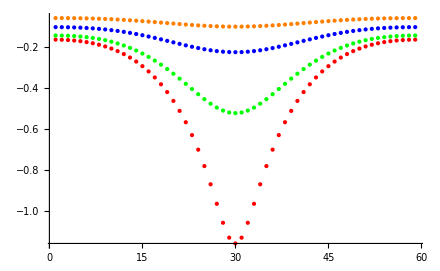
```mathematica
-Graphics-(*ϵ1=10, ϵ2=5*)
```

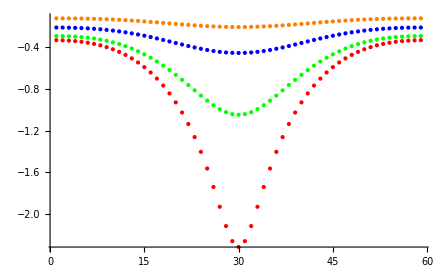
```mathematica
-Graphics-(*ϵ1=5, ϵ2=5 AND ϵ1=10, ϵ2=10*)
```

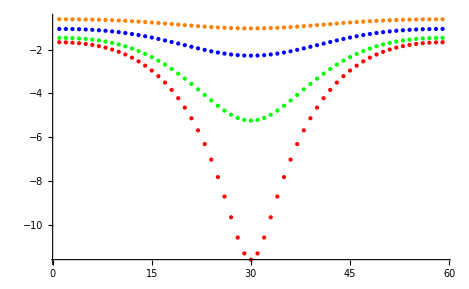
```mathematica
-Graphics-(*ϵ1=1, ϵ2=5*)
```

```mathematica
minvoltage = 2.25(ϵ2/ϵ1)
```

```mathematica
plotList//MatrixForm
halfSpaceVoltage=Flatten[Table[
{i,Floor[(MM+1)/2]-j+1,potential[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,Floor[(MM+1)/2],1,-1}
],1];(*Gets voltage from left half space, then reflects it to right half space and sets origin to (1,1)*)
halfSpaceVoltage//MatrixForm
ListPlot3D[halfSpaceVoltage,PlotRange->All]
```

(1 | 1 | -0.361084
1 | 2 | -0.381837
1 | 3 | -0.425635
1 | 4 | -0.472623
1 | 5 | -0.496723
1 | 6 | -0.482322
1 | 7 | -0.439318
1 | 8 | -0.387934
2 | 1 | -0.255887
2 | 2 | -0.256272
2 | 3 | -0.266248
2 | 4 | -0.281383
2 | 5 | -0.292209
2 | 6 | -0.292316
2 | 7 | -0.28264
2 | 8 | -0.267153
3 | 1 | -0.173321
3 | 2 | -0.16971
3 | 3 | -0.169263
3 | 4 | -0.172855
3 | 5 | -0.177759
3 | 6 | -0.181119
3 | 7 | -0.181638
3 | 8 | -0.178307
4 | 1 | -0.10725
4 | 2 | -0.104068
4 | 3 | -0.101666
4 | 4 | -0.101758
4 | 5 | -0.103921
4 | 6 | -0.106895
4 | 7 | -0.109313
4 | 8 | -0.10943
5 | 1 | -0.0512952
5 | 2 | -0.0496847
5 | 3 | -0.0481383
5 | 4 | -0.047729
5 | 5 | -0.0485465
5 | 6 | -0.0501138
5 | 7 | -0.0516634
5 | 8 | -0.052116
1 | 9 | -0.361084
2 | 9 | -0.255887
3 | 9 | -0.173321
4 | 9 | -0.10725
5 | 9 | -0.0512952)

(1 | 1 | -0.496723
1 | 2 | -0.472623
1 | 3 | -0.425635
1 | 4 | -0.381837
1 | 5 | -0.361084
2 | 1 | -0.292209
2 | 2 | -0.281383
2 | 3 | -0.266248
2 | 4 | -0.256272
2 | 5 | -0.255887
3 | 1 | -0.177759
3 | 2 | -0.172855
3 | 3 | -0.169263
3 | 4 | -0.16971
3 | 5 | -0.173321
4 | 1 | -0.103921
4 | 2 | -0.101758
4 | 3 | -0.101666
4 | 4 | -0.104068
4 | 5 | -0.10725
5 | 1 | -0.0485465
5 | 2 | -0.047729
5 | 3 | -0.0481383
5 | 4 | -0.0496847
5 | 5 | -0.0512952)

-Graphics3D-